```mathematica
cols=Short[ColorData[109,"ColorList"],4];
col1=cols[[1,8]]
col2=cols⟦1,9⟧
col3=cols[[1,10]]
col4=cols[[1,7]]
col5=cols⟦1,5⟧
col6=cols⟦1,14⟧
```

RGBColor[1., 0.325204, 0.406504]

RGBColor[0., 0.786874, 0.739379]

RGBColor[1., 0.520437, 0.]

RGBColor[0.238758, 0.610466, 1.]

RGBColor[0.893126, 0.4, 0.767184]

RGBColor[0, 0.7226017980018511, 0.9321946059944466]

```mathematica
(*Funtions*)
δ[p_,q_]:=Subscript[δ, min]+(Subscript[δ, 0]-Subscript[δ, min])*Exp[-(p-q)^2/(2*Subscript[k, 1]^2)];
ρ[p_]:=Subscript[ρ, min]+(Subscript[ρ, 0]-Subscript[ρ, min])*Exp[-p^2/(2*Subscript[k, 2]^2)];
μ[q_]:=Subscript[μ, min]+(Subscript[μ, 0]-Subscript[μ, min])*Exp[-q^2/(2*Subscript[k, 3]^2)];
G1[ϕ1_,p_,q_,u_,v_]:=ρ[ϕ1]*(1-u/κ)-(δ[ϕ1,q]*v)/(1+δ[ϕ1,q]*γ*u);
G2[ϕ2_,p_,q_,u_,v_]:=(α*δ[p,ϕ2]*u)/(1+δ[p,ϕ2]*γ*u)-μ[ϕ2];
G3[ϕ1_,p_,q_,u_,v_]:=ρ[ϕ1]*(1-u/κ)*(u/τ-1)-(δ[ϕ1,q]*v)/(1+δ[ϕ1,q]*γ*u);
G11[p_,q_,u_,v_]:=D[G1[ϕ1,p,q,u,v],{ϕ1,1} ] /.ϕ1->p;
G22[p_,q_,u_,v_]:=D[G2[ϕ2,p,q,u,v],{ϕ2,1} ] /.ϕ2->q;
G33[p_,q_,u_,v_]:=D[G3[ϕ1,p,q,u,v],{ϕ1,1} ] /.ϕ1->p;
```

```mathematica
Subscript[ρ, 0]=0.75;Subscript[ρ, min]=0.25;κ=35;Subscript[δ, 0]=0.15;Subscript[δ, min]=0.05;γ=0.02;α=0.7;Subscript[μ, 0]=2.0;Subscript[μ, min]=1.0;Subscript[k, 1]=1.0;Subscript[k, 2]=1.0;Subscript[k, 3]=1.0;f=0.5;
sol=NDSolve[{u'[t]==u[t]*G1[p[t],p[t],q[t],u[t],v[t]],p'[t]==f*G11[p[t],q[t],u[t],v[t]],v'[t]==v[t]*G2[q[t],p[t],q[t],u[t],v[t]],q'[t]==f*G22[p[t],q[t],u[t],v[t]],u[0]==3,p[0]==2,v[0]==3,q[0]==-2},{u,p,v,q},{t,0,10000},AccuracyGoal->8,PrecisionGoal->6,MaxSteps->10^6];
τ=1;
sol2=NDSolve[{u'[t]==u[t]*G3[p[t],p[t],q[t],u[t],v[t]],p'[t]==f*G33[p[t],q[t],u[t],v[t]],v'[t]==v[t]*G2[q[t],p[t],q[t],u[t],v[t]],q'[t]==f*G22[p[t],q[t],u[t],v[t]],u[0]==3,p[0]==2,v[0]==3,q[0]==-2},{u,p,v,q},{t,0,20000},AccuracyGoal->8,PrecisionGoal->6,MaxSteps->10^6];
```

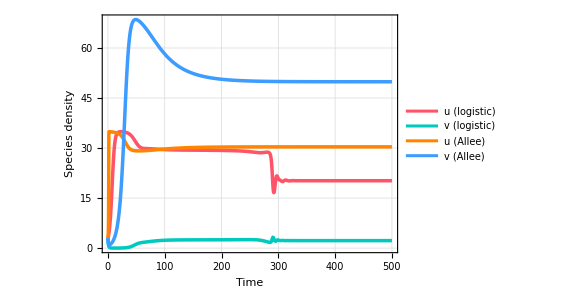

```mathematica
(*---fig 4A:Species densities---*)
A11=Plot[Evaluate[{u[t]/. sol,v[t]/. sol,u[t]/. sol2,v[t]/. sol2}],{t,0,500},PlotRange->{All,All},PlotLegends->Placed[LineLegend[{"u (logistic)","v (logistic)","u (Allee)","v (Allee)"},LegendLayout->{"Row",2}],{0.65,0.85}],LabelStyle->{FontSize->16},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{"Time","Species density"},PlotStyle->{{col1,Thickness[0.006]},{col2,Thickness[0.006]},{col3,Thickness[0.006]},{col4,Thickness[0.006]}},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.5],Dotted,Thickness[0.002]],AspectRatio->1.5/2.1(*,Epilog->{Style[Text["A",{950,45}],FontSize->20,Background->White]},*),ImageSize->420]
```

```mathematica
G111[t_,ϕ_]:=G1[ϕ,p[t]/. sol[[1]],q[t]/. sol[[1]],u[t]/. sol[[1]],v[t]/. sol[[1]]];
G222[t_,ϕ_]:=G2[ϕ,p[t]/. sol[[1]],q[t]/. sol[[1]],u[t]/. sol[[1]],v[t]/. sol[[1]]];
(*-----------------------------fig 4C-------------------------------*)
j1=Plot3D[G111[t,ϕ],{ϕ,-4,4},{t,0,1000},PlotRange->{{-4,4},{0,500},{-1.3,All}},Mesh->{4,4},MeshStyle->{White,White},Boxed->False,BoundaryStyle->None,Axes->True,AxesStyle->Directive[Black,Thickness[0.003]],AxesLabel->{"Evolutionary strategy","Time","Fitness"},LabelStyle->Directive[Black,16],BoxRatios->{1,1,1},PlotStyle->{col5,Opacity[0.6]},(*PlotPoints->500,*)ClippingStyle->None,(*PlotLabel->Style["B",20],*)ImageSize->450];

(*-----------------------------fig 4D-------------------------------*)
j2=Plot3D[G222[t,ϕ],{ϕ,-4,4},{t,0,500},PlotRange->{{-4,4},{0,500},{-1.3,All}},Mesh->{4,4},MeshStyle->{Black,Black},Boxed->False,BoundaryStyle->None,PlotStyle->{col6, Opacity[0.6]}(*,PlotPoints->50*)];

(*------------------solution on landscapes-----------------------------*)
G1111[t_]:=G1[p[t]/. sol[[1]],p[t]/. sol[[1]],q[t]/. sol[[1]],u[t]/. sol[[1]],v[t]/. sol[[1]]];
G2222[t_]:=G2[q[t]/. sol[[1]],p[t]/. sol[[1]],q[t]/. sol[[1]],u[t]/. sol[[1]],v[t]/. sol[[1]]];

(*-----------------strategy on landscape prey--------------------*)
k1=ParametricPlot3D[{p[t]/. sol[[1]],t,G1111[t]+0.008},{t,0,500},PlotRange->{{-3,3},{0,500},All},PlotStyle->{Red,Thickness[0.006]},BoxRatios->{1,1,1},Boxed->False];

(*-----------------strategy on landscape predator--------------------*)
k2=ParametricPlot3D[{q[t]/. sol[[1]],t,G2222[t]+0.01},{t,0,500},PlotRange->{{-1,1},{0,500},All},PlotStyle->{Blue,Thickness[0.006]},BoxRatios->{1,1,1},Boxed->False,ImageSize->Large];
k3=Show[j1,j2,k1,k2,ViewPoint->{1,1.7,1}]
```

-Graphics3D-

```mathematica
G111[t_,ϕ_]:=G3[ϕ,p[t]/. sol2[[1]],q[t]/. sol2[[1]],u[t]/. sol2[[1]],v[t]/. sol2[[1]]];
G222[t_,ϕ_]:=G2[ϕ,p[t]/. sol2[[1]],q[t]/. sol2[[1]],u[t]/. sol2[[1]],v[t]/. sol2[[1]]];

(*-----------------------------fig 4G-------------------------------*)
j1=Plot3D[G111[t,ϕ],{ϕ,-5,5},{t,0,500},PlotRange->{{-4,4},{0,500},{-6,5}},Mesh->{4,4},MeshStyle->{White,White},Boxed->False,BoundaryStyle->None,Axes->True,AxesStyle->Directive[Black,Thickness[0.003]],AxesLabel->{"Evolutionary strategy","Time","Fitness"},LabelStyle->Directive[Black,16],BoxRatios->{1,1,1},PlotStyle->{col5,Opacity[0.6]},(*PlotPoints->500,*)ClippingStyle->None,(*PlotLabel->Style["C",20],*)ImageSize->450];

(*-----------------------------fig 4H-------------------------------*)
j2=Plot3D[G222[t,ϕ],{ϕ,-5,5},{t,0,500},PlotRange->{{-4,4},{0,500},All},Mesh->{4,4},MeshStyle->{Black,Black},Boxed->False,BoundaryStyle->None,PlotStyle->{col6, Opacity[0.6]}(*,PlotPoints->400*)];

(*-----------------------solution on landscape-----------------------*)
G1111[t_]:=G3[p[t]/. sol2[[1]],p[t]/. sol2[[1]],q[t]/. sol2[[1]],u[t]/. sol2[[1]],v[t]/. sol2[[1]]];
G2222[t_]:=G2[q[t]/. sol2[[1]],p[t]/. sol2[[1]],q[t]/. sol2[[1]],u[t]/. sol2[[1]],v[t]/. sol2[[1]]];

(*-----------------strategy on landscape prey--------------------*)
k1=ParametricPlot3D[{p[t]/. sol2[[1]],t,G1111[t]+0.001},{t,0,500},PlotRange->{{-1,1},{0,500},All},PlotStyle->{Red,Thickness[0.006]},BoxRatios->{1,1,1},Boxed->False];

(*-----------------strategy on landscape predator--------------------*)
k2=ParametricPlot3D[{q[t]/. sol2[[1]],t,G2222[t]+0.01},{t,0,500},PlotRange->{{-4,4},{0,500},All},PlotStyle->{Blue,Thickness[0.006]},BoxRatios->{1,1,1},Boxed->False];
k4=Show[j1,j2,k1,k2,ViewPoint->{0.8,1.5,1}]
```

-Graphics3D-

```mathematica
fig=Grid[{{Style["A: Eco-evolutionary dynamics",25],Style["B: Logistic growth landscape",25],Style["C: Allee effect landscape",25]},{A11,k3,k4}}]
```

A: Eco-evolutionary dynamics | B: Logistic growth landscape | C: Allee effect landscape
-Graphics- | -Graphics3D- | -Graphics3D-

```mathematica
Export[SystemDialogInput["FileSave","normal_2(0.75).pdf"],fig,ImageResolution->350,"CompressionLevel"->0]
```

C:\Users\SANTANA\Dropbox\SANTANA\P7_G function\Mondal_allee effect\normal_2(0.75).pdf